# Pressure-coupled chain of scatterers

### Preamble

```mathematica
ClearAll["Global`*"];(* clears all functions *)
SetDirectory[NotebookDirectory[]]; (* or else the default directory is Directory[]*)
myEliminate[sys_,var_]:=Module[{sol},
sol=Solve[sys[[1]],var][[1]];
sys[[2;;-1]]/.sol
];
Needs["ToMatlab`"];
```

### Parameters

```mathematica
mms=6.7*^-4; 
rms=0.26*0.2;
cmc=2.13*^-4;
fres = 1/(2*Pi*Sqrt[mms*cmc])

sd=12*^-4;(* m^2 diaphragm surface *)
s=0.05*0.05; (*  m^2 duct cross section*)
rho0=1.184;(*[kg/m^3]*)
c0=346;(*%[m/s]*)
a=0.2806;(*[m]*)
kk = 1*(sd); (*POSITIVE Coupling*)
f0 = c0/a (*cutoff frequency*)
(*Clear[Mms,Rms,Cmc,fres,sd,S,rho0,c0,a,kk,f0]*)
zs[k_] := (ⅈ  k c0)*mms + rms + 1/( (ⅈ  k c0)*cmc);
zr:= rho0 c0 sd/s;
```

421.301

1233.07

### Speaker mechanical impedance

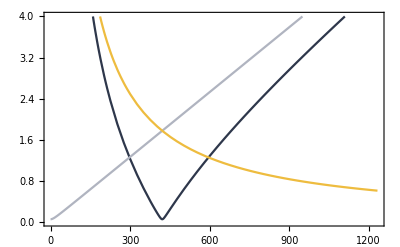

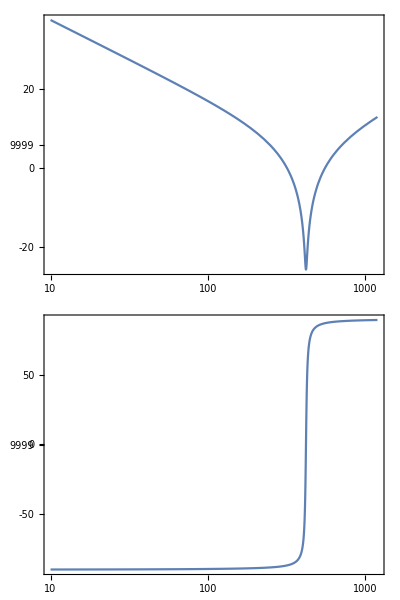

```mathematica
Zms[freq_]:= (I*2*Pi*freq)*mms + rms + 1/((I*2*Pi*freq)*cmc);
ZmsAbv[freq_]:= (I*2*Pi*freq)*mms + rms ;
ZmsBlw[freq_]:=  rms + 1/((I*2*Pi*freq)*cmc);

Plot[{Abs[Zms[freq] ] ,Abs[ZmsAbv[freq]] ,Abs[ZmsBlw[freq] ]},{freq,0.1,f0},PlotRange->{{0,f0},{0,4}},PlotStyle->{ColorData["GrayYellowTones",0],ColorData["GrayYellowTones",0.5],ColorData["GrayYellowTones",1]},Frame->True]
BodePlot[Zms[f],{f,10,1200}]
```

### Transfer Matrix

#### Wave Guide section

```mathematica
m1[k_] := ({{Exp[-I k a/4], 0}, {0, Exp[+I k a/4]}});
```

#### Active section

```mathematica
(*pressure_coupling__TM.nb*)
m2[k_]:= ({{((-1+ⅇ^(ⅈ a k)) (kk-sd) (kk+sd) zr^2+4 zs[k] (ⅇ^((ⅈ a k)/2) kk zr-sd zr+zs[k]))/(2 zs[k] ((-1+ⅇ^(ⅈ a k)) kk zr+2 ⅇ^((ⅈ a k)/2) zs[k])), (zr ((kk-sd) (kk+sd) zr Sin[(a k)/2]-2 ⅈ (kk-sd Cos[(a k)/2]) zs[k]))/(2 (kk zr Sin[(a k)/2]-ⅈ zs[k]) zs[k])}, {(zr ((-kk^2+sd^2) zr Sin[(a k)/2]+2 ⅈ (kk-sd Cos[(a k)/2]) zs[k]))/(2 (kk zr Sin[(a k)/2]-ⅈ zs[k]) zs[k]), -((-1+ⅇ^(ⅈ a k)) (kk-sd) (kk+sd) zr^2+4 ⅇ^((ⅈ a k)/2) kk zr zs[k]-4 ⅇ^(ⅈ a k) zs[k] (sd zr+zs[k]))/(2 zs[k] ((-1+ⅇ^(ⅈ a k)) kk zr+2 ⅇ^((ⅈ a k)/2) zs[k]))}});
```

#### Total transfer matrix

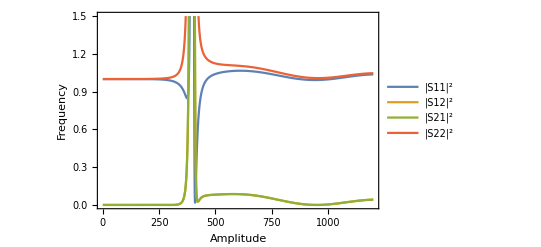

```mathematica
m[k_]:=m1[k].m2[k].m1[k];(*full Transfer Matrix*)
m11[k_]:= m[k][[1,1]]//FullSimplify;
m12[k_]:= m[k][[1,2]]//FullSimplify ;
m21[k_]:= m[k][[2,1]] //FullSimplify;
m22[k_]:= m[k][[2,2]] //FullSimplify; 
m[k]//MatrixForm;

(*Define the full Transfer Matrix*)m[k_]:=m1[k].m2[k].m1[k];

(*Compute the square of the Transfer Matrix*)
mSquared[k_]:=m[k].m[k];

(*Extract and simplify the elements of the squared matrix*)
mSquared11[k_]:=mSquared[k][[1,1]]//FullSimplify;
mSquared12[k_]:=mSquared[k][[1,2]]//FullSimplify;
mSquared21[k_]:=mSquared[k][[2,1]]//FullSimplify;
mSquared22[k_]:=mSquared[k][[2,2]]//FullSimplify;

Plot[{
Abs[mSquared11[2*Pi*freq/c0]]^2,
Abs[mSquared12[2*Pi*freq/c0]]^2,
Abs[mSquared21[2*Pi*freq/c0]]^2,
Abs[mSquared22[2*Pi*freq/c0]]^2
},{freq,0.1,1200},PlotRange->{{0,1200},{0,1.5}},Frame->True, PlotLegends->{"|S11|^2","|S12|^2","|S21|^2","|S22|^2"},AxesLabel->{"Amplitude","Frequency"}]
```

### Scattering Matrix

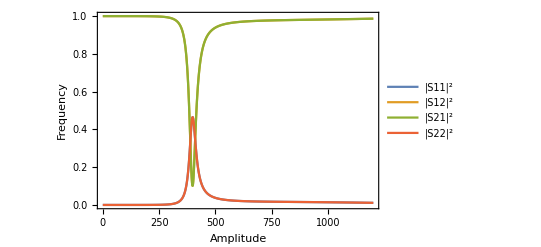

```mathematica
(*SS[k_]:= {{-M21[k]/M22[k],1/M22[k]},{M11[k]-M12[k]*M21[k]/M22[k],M12[k]/M22[k]}}*)
s11[k_]:= -m21[k]/m22[k];
s12[k_]:=1/m22[k];
s21[k_]:=m11[k]-m12[k]*m21[k]/m22[k];
s22[k_]:=m12[k]/m22[k];
ss[k_]:={{s11[k],s12[k]},{s21[k],s22[k]}} ;

(*MatrixForm[SS[k]]//FullSimplify*)

Plot[{
Abs[s11[2*Pi*freq/c0]]^2,
Abs[s12[2*Pi*freq/c0]]^2,
Abs[s21[2*Pi*freq/c0]]^2,
Abs[s22[2*Pi*freq/c0]]^2
},{freq,0.1,1200},PlotRange->{{0,1200},{0,1}},Frame->True, PlotLegends->{"|S11|^2","|S12|^2","|S21|^2","|S22|^2"},AxesLabel->{"Amplitude","Frequency"}]
```

### Effective density and bulk modulus

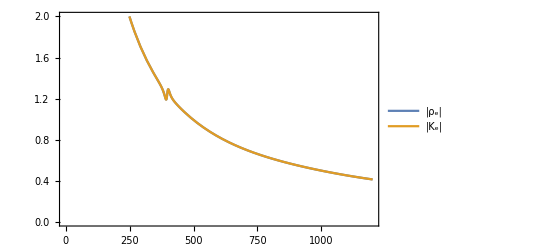

```mathematica
ze[k_]:= Sqrt[((1+s11[k])^2-s21[k]^2)/((1+s11[k])^2-s21[k]^2)];(* Effective impedance plus-minus*)
n[k_]:= ArcCos[(1-s11[k]^2-s21[k]^2)/(2 s21[k])+2π]/(k a);(*Effective refractive index plus-minus*)

Plot[{
Abs[n[2*Pi*freq/c0]*ze[2*Pi*freq/c0]],
Abs[n[2*Pi*freq/c0]/ze[2*Pi*freq/c0]]
},{freq,0.1,1200},PlotRange->{{0,1200},{0,2}},Frame->True, PlotLegends->{"|ρ_e|","|K_e|"}]
```

### Dispersion

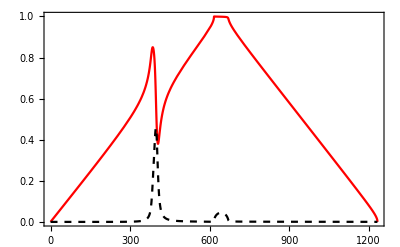

```mathematica
trFunc[k_]:= Tr[m[k]]/2 ;
(*TrFunc[k_]:= Tr[M[k]]- Sqrt[Tr[M[k]]^2-4*Det[Tr[M[k]]]];*)
(*TraceM1[k_]:= (M11[k]+ M22[k])/2- Sqrt[((M11[k]+ M22[k])/2)^2+M12[k]+ M21[k]];*)
q[k_] :=ArcCos[ trFunc[k]]/a//FullSimplify;
q[k]//MatrixForm;
(*q[kk];ToMatlab[%];*)
Plot[{Re[q[2*Pi*freq/c0]*a/Pi],Abs[Im[q[2*Pi*freq/c0]*a/Pi]]},{freq,0.1,f0},PlotRange->{{0,f0},{0,1}},PlotStyle->{Red,{Black,Dashed},Thick},Frame->True]
```

### Energy conserving = S-matrix is unitary

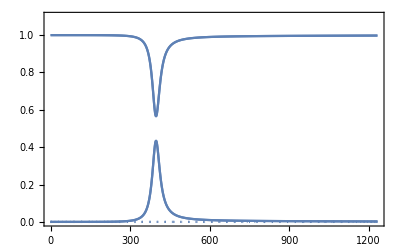

```mathematica
ReImPlot[ss[2*Pi*freq/c0].Transpose[Conjugate[ss[2*Pi*freq/c0]]],{freq,0.1,f0},PlotRange->{{0,f0},{0,1.1}},Frame->True]
```

### SU (1, 1) group?

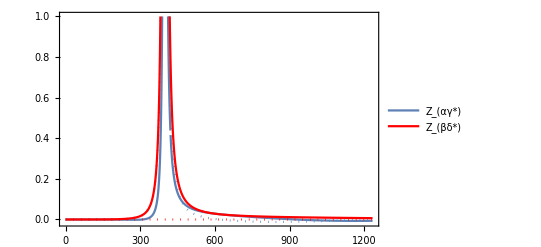

```mathematica
(*ReImPlot[M11[2*Pi*freq/c0]*M22[2*Pi*freq/c0] - M12[2*Pi*freq/c0]*M21[2*Pi*freq/c0] ,{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}},Frame->True]*)
range = Range[0.1,f0];(*averaging range*)

alphaGamma[freq_]:= m11[2*Pi*freq/c0]-Conjugate[m22[2*Pi*freq/c0]];
meanAlphaGamma := Mean[alphaGamma /@ range ];
stdAlphaGamma:= StandardDeviation[alphaGamma /@ range ]

betaDelta[freq_]:= m12[2*Pi*freq/c0]-Conjugate[m21[2*Pi*freq/c0]];
meanBetaDelta := Mean[betaDelta /@ range ];
stdBetaDelta:= StandardDeviation[betaDelta/@ range ];

zAlpha[freq]= (alphaGamma[freq]- 0*meanAlphaGamma)/stdAlphaGamma;
zBeta[freq]  = (betaDelta[freq]- 0*meanBetaDelta)/stdBetaDelta;

p1 = ReImPlot[zAlpha[freq],{freq,0.1,f0},PlotRange->{{0,f0},{-1,1}},Frame->True,PlotLegends->LineLegend[{"Z_(αγ*)"}]];
p2 = ReImPlot[zBeta[freq],{freq,0.1,f0},PlotRange->{{0,f0},{-1,1}},Frame->True,PlotLegends->LineLegend[{"Z_(βδ*)"}],PlotStyle->Red];
Show[p1,p2, PlotRange->All]
```

### Topology

```mathematica
(* REMINDER: k: is the free field wave vector and q: is the Floquet wave number*) 
ev[k_]:=Eigenvectors[({{aa, bb}, {cc, dd}})]/.{aa->m11[k],bb->m12[k],cc->m21[k],dd->m22[k]}//Simplify;
ev1[k_]:=ev[k][[1,1]]//Simplify; (*first eigenvector*)


u1[k_,x_,q_]:= ev1[k]*Exp[-I q x]//Simplify;
du1[k_,x_,q_]:=D[u1[k,x,q],q]//Simplify;
bc1[k_,x_,q_]:= Conjugate[u1[k,x,q]]*du1[k,x,q]//Simplify;(*Berry Connection*)


deltaPhi1[k_,q_] := Arg[Integrate[bc1[k,x,q],{x,0,a/2}]]//Simplify


(*thetaZak1[k_]= Integrate[Mod[deltaPhi1[k,q],2*Pi] ,{q,-(Pi/a),Pi/ a}];*)

(*
ReImPlot[thetaZak1[2*Pi*freq/c0],{freq,0.1,f0},Frame->True]

ev = Table[Eigenvectors[m[2*Pi*freq/c0]],{freq,0.1,f0,10}]//FullSimplify;
ev[[4]]//FullSimplify
*)
```

```mathematica
(*
alphaR[k_]:= Re[m11[k]]
alphaI[k_]:=Im[m11[k]]
betaR[k_]:=Re[m21[k]]
betaI[k_]:=Im[m21[k]]

coneplot = Plot3D[{Sqrt[x^2+y^2],-Sqrt[x^2+y^2]},{x,-2,2},{y,-2,2},
RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic,
ColorFunction->"RustTones",
PlotStyle->Opacity[0.5],
Mesh-> False,
Boxed->False,
Axes->False,
AxesOrigin->{0,0,0},
AxesStyle->Opacity[1],
TicksStyle->None,
AxesLabel->{Style[hi,16],Style[y,16],Style[z,16]},
ViewPoint->{Pi,Pi/2,2},Background->None]
(*Export["cone.png",coneplot,Background->None,ImageResolution-> 300]*)

Directory[]
*)
```